## Fonction

```mathematica
Quit
```

```mathematica
Poisson[lambda_,i_]:=Exp[(-lambda)]*(lambda^i/(i!));
HyperGeo[n_,Nn_,m_,i_]:=Binomial[m,i]Binomial[Nn-m,n-i]/Binomial[Nn,n];
Geo[n_,p_]:=(1-p)^(n-1)p;
Bin[n_,p_,x_]:=Binomial[n,x]*p^x*(1-p)^(n-x);
BinNeg[n_,p_,r_]:=Binomial[n-1,r-1]p^r (1-p)^(n-r);
Centre[x_,mu_,sigma_]:=(x-mu)/sigma;
Pnorm[z_]:=N[CDF[NormalDistribution[0,1],z]];
Qnorm[p_]:=N[InverseCDF[NormalDistribution[0,1],p]];
(*\[Distributed]*)
```

### Pour les conditionnelles

```mathematica
Quit
```

```mathematica
Remove[P];
Unprotect@Intersection;
Intersection[A_Symbol,B_Symbol]:={A,B}
Intersection[A_Not,B_Symbol]:={A,B}
Intersection[A_Symbol,B_Not]:={A,B}
P[Int_List/;Length@Int==2]:=P[Int[[2]]\[Conditioned]Int[[1]]] P[Int[[1]]]
(*//P(B) given knowledge of P(A)//*)
P[B_,A_]:=If[NumericQ@B,B,P[B\[Conditioned]A] P[A]+P[B\[Conditioned]Not@A] P[Not@A]]
P[Not@B_,A_: 1]:=If[NumericQ@A,1-P[B],1-P[B,A]]
P[A_\[Conditioned]B_]:=P[A∩B]/P[B,A]
P[Not@A_\[Conditioned]B_]:=1-P[A\[Conditioned]B];
```

# Examen Intra

## Question #1

```mathematica
Integrate[(1-x^2),{x,-1,1}]
```

Inverse::matsq: Argument 4/3 at position 1 is not a non-empty square matrix.

Inverse[4/3]

```mathematica
f[x_]:=(3/4)(1-x^2)
Integrate[f[x] x,{x,-1,1}]
Integrate[f[x]x^2,{x,-1,1}]
```

0

1/5

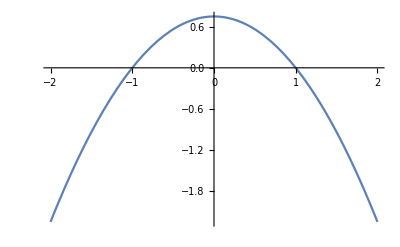

27/32

1/2

11/32

```mathematica
Plot[f[x],{x,-2,2}]
Fx[a_]:=Integrate[f[x],{x,-1,a}]
FullSimplify@%
Fx[1/2]
Fx[0]
Fx[1/2]-Fx[0]
```

## Question #2

```mathematica
mu=300;
sigma=20;
Centre[320,mu,sigma]
N@Probability[x>1,x\[Distributed]NormalDistribution[0,1]]
Qnorm[0.98]
% sigma+mu
NProbability[4<x<=5,x\[Distributed]ExponentialDistribution[10]]


Probability[x≥31,x\[Distributed]ExponentialDistribution[10]]
N[Exp[-50]-Exp[-40]]
```

1

1.

2.05375

341.075

1.

0

-4.24816×10^-18

## Question #3

## Question #4

## Question #5

## Question #6